```mathematica
Clear["Global`*"]
```

```mathematica
g=9.80665;
m=80;
k=10.1;
Vo=0;
Yo=5000;
yf[t_]:=(-g m^2)/k^2 ⅇ^(-k/m t)-(g m)/k t+(g m^2)/k^2+Yo;
vf[t_]:=(g m)/k ⅇ^(-k/m t)-(m g)/k;
af[t_]:=-g ⅇ^(-k/m t);
y[t_]:=-1/2 g t^2+Vo t+Yo;
v[t_]:=-g t + Vo;
a[t_]:=-g;
yyf=Plot[{yf[t],y[t]},{t,0,80},PlotRange->{{0,80},{0,5000}},PlotLegends->{"y avec frottement","y sans frottement"},PlotLabel->"Comparaison y[t]"];
vvf=Plot[{vf[t],v[t]},{t,0,80},PlotLegends->{"v avec frottement","v sans frottement"},PlotLabel->"Comparaison y'[t]"];
aaf=Plot[{af[t],a[t]},{t,0,80},PlotLegends->{"a avec frottement","a sans frottement"},PlotLabel->"Comparaison y''[t]"];
afvf=Plot[{af[t],vf[t]},{t,0,80},PlotLegends->{"a avec frottement","v avec frottement"},PlotLabel->"Comparaison y'[t] & y''[t]"];
```

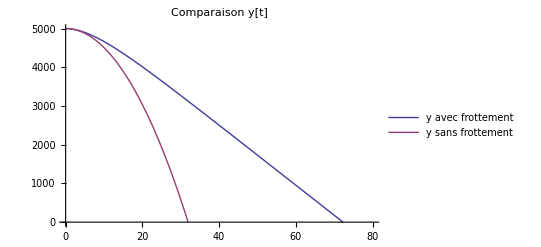
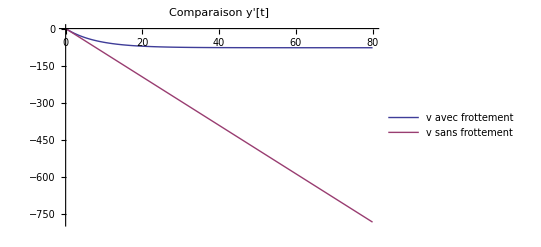
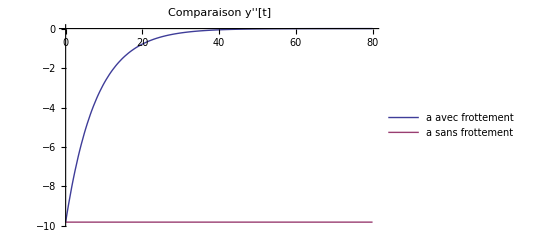
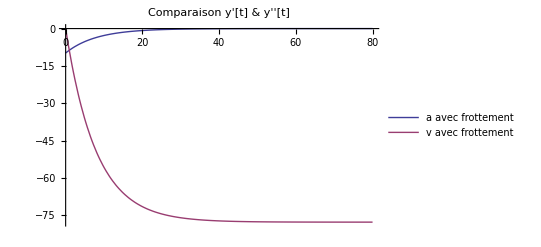

```mathematica
{yyf,vvf,aaf,afvf}
```